```mathematica
TableForm[Table[With[{full=Binomial[n,2],maximal=(3n-6)},
{n,full,maximal,full-maximal,full-maximal-n+1}
],{n,3,50}]]
```

3 | 3 | 3 | 0 | -2
4 | 6 | 6 | 0 | -3
5 | 10 | 9 | 1 | -3
6 | 15 | 12 | 3 | -2
7 | 21 | 15 | 6 | 0
8 | 28 | 18 | 10 | 3
9 | 36 | 21 | 15 | 7
10 | 45 | 24 | 21 | 12
11 | 55 | 27 | 28 | 18
12 | 66 | 30 | 36 | 25
13 | 78 | 33 | 45 | 33
14 | 91 | 36 | 55 | 42
15 | 105 | 39 | 66 | 52
16 | 120 | 42 | 78 | 63
17 | 136 | 45 | 91 | 75
18 | 153 | 48 | 105 | 88
19 | 171 | 51 | 120 | 102
20 | 190 | 54 | 136 | 117
21 | 210 | 57 | 153 | 133
22 | 231 | 60 | 171 | 150
23 | 253 | 63 | 190 | 168
24 | 276 | 66 | 210 | 187
25 | 300 | 69 | 231 | 207
26 | 325 | 72 | 253 | 228
27 | 351 | 75 | 276 | 250
28 | 378 | 78 | 300 | 273
29 | 406 | 81 | 325 | 297
30 | 435 | 84 | 351 | 322
31 | 465 | 87 | 378 | 348
32 | 496 | 90 | 406 | 375
33 | 528 | 93 | 435 | 403
34 | 561 | 96 | 465 | 432
35 | 595 | 99 | 496 | 462
36 | 630 | 102 | 528 | 493
37 | 666 | 105 | 561 | 525
38 | 703 | 108 | 595 | 558
39 | 741 | 111 | 630 | 592
40 | 780 | 114 | 666 | 627
41 | 820 | 117 | 703 | 663
42 | 861 | 120 | 741 | 700
43 | 903 | 123 | 780 | 738
44 | 946 | 126 | 820 | 777
45 | 990 | 129 | 861 | 817
46 | 1035 | 132 | 903 | 858
47 | 1081 | 135 | 946 | 900
48 | 1128 | 138 | 990 | 943
49 | 1176 | 141 | 1035 | 987
50 | 1225 | 144 | 1081 | 1032

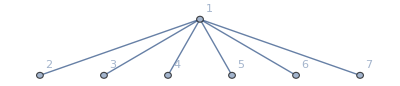
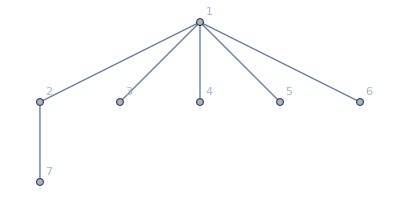
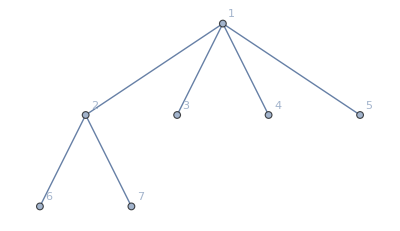
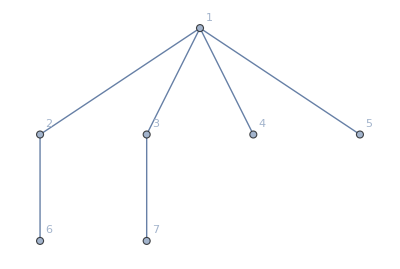
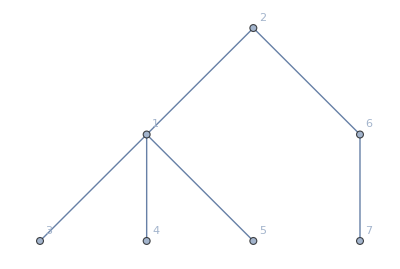
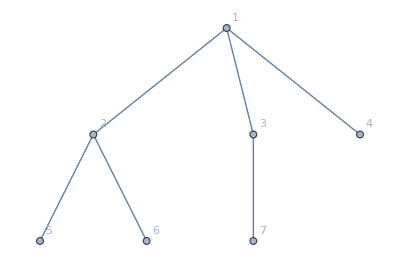
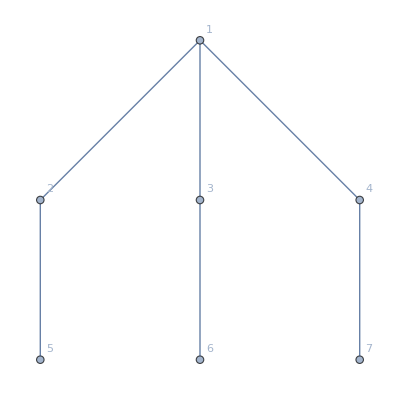
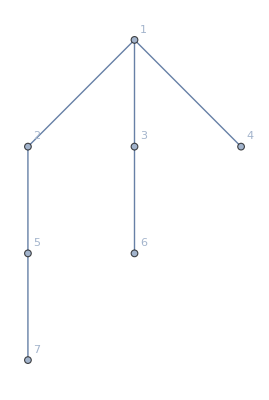
{-Graphics-
7,-Graphics-
210,-Graphics-
420,-Graphics-
1260,-Graphics-
840,-Graphics-
2520,-Graphics-
840,-Graphics-
5040,-Graphics-
630,-Graphics-
2520,-Graphics-
2520}

```mathematica
Map[Framed[TableForm[#,TableAlignments->Center]]&,Tally[Select[Table[Graph[Range[7],set,VertexLabels->"Name"],{set,Subsets[Subsets[Range[7],{2}],{6}]}],ConnectedGraphQ[#]&],IsomorphicGraphQ[#1,#2]&]]
```

```mathematica
Table[VertexCount[Graph[plantri[[k]]]],{k,1,10}]
```

{12,14,15,16,16,16,17,17,17,17}

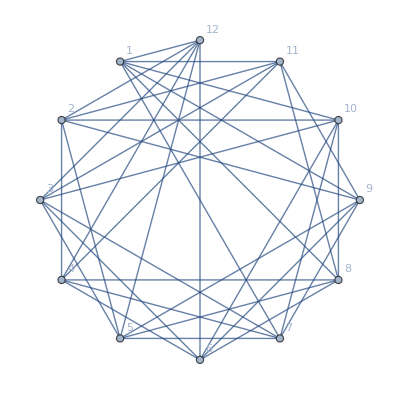

```mathematica
GraphComplement[Graph[plantri[[1]]],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]
```